```mathematica
bin=Databin["vZA0S3eZ"]
```

Databin[…]

```mathematica
Databin[…]
```

Databin[…]

## Databin Visualization

Visualize all data by calling the bin by the name defined above. Select only the correct trials. This means filtering out the practice trials and the marker trials.

```mathematica
surveyData=Dataset[bin];
filteredData=surveyData[Select[#Numerator>0&]];
```

## Calculating RT

Take the two columns of time response “StimuliPresTime” and “TimeSubmitted” to calculate reaction time. Reaction time is the time from when the stimuli was presented (“StimuliPresTime”) to when the button was clicked (which submits the data to the loud “TimeSubmitted”).  Since time submitted comes later, being the longer time, we will subtract the time the stimuli was presented from it.The result is a list of DateObjets. We will transform these into numbers.

```mathematica
stimuliPresTime = filteredData[All,"StimuliPresTime"];
timeSubmitted =  filteredData[All,"TimeSubmitted"];
DateObjRTs=Table[(timeSubmitted[[i]]-stimuliPresTime[[i]]),{i,Length[stimuliPresTime]}];
RTs=Table[DateObjRTs[[x,1]],{x,Length[DateObjRTs]}];
```

## Calculating Magnitudes

Extract the numerator and denominator columns from the filteredData dataset separately.Calculate the real value magnitude of each fraction (numerator divided by denominator). N forces the value to be presented in real form instead of fraction form. Create a table with a magnitude and its reaction time for each of the magnitudes and RTs there are.

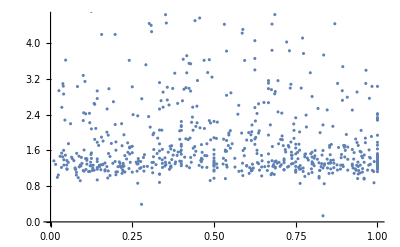

```mathematica
numerators= filteredData[All,"Numerator"];
denominators=filteredData[All,"Denominator"];
magnitudes=Table[N[numerators[[i]]/denominators[[i]]],{i,Length[numerators]}];
RTbyMag=Table[{magnitudes[[i]],RTs[[i]]},{i,Length[magnitudes]}];
ListPlot[{RTbyMag},DataRange->{0,1}]
```

## Calculating Accuracy

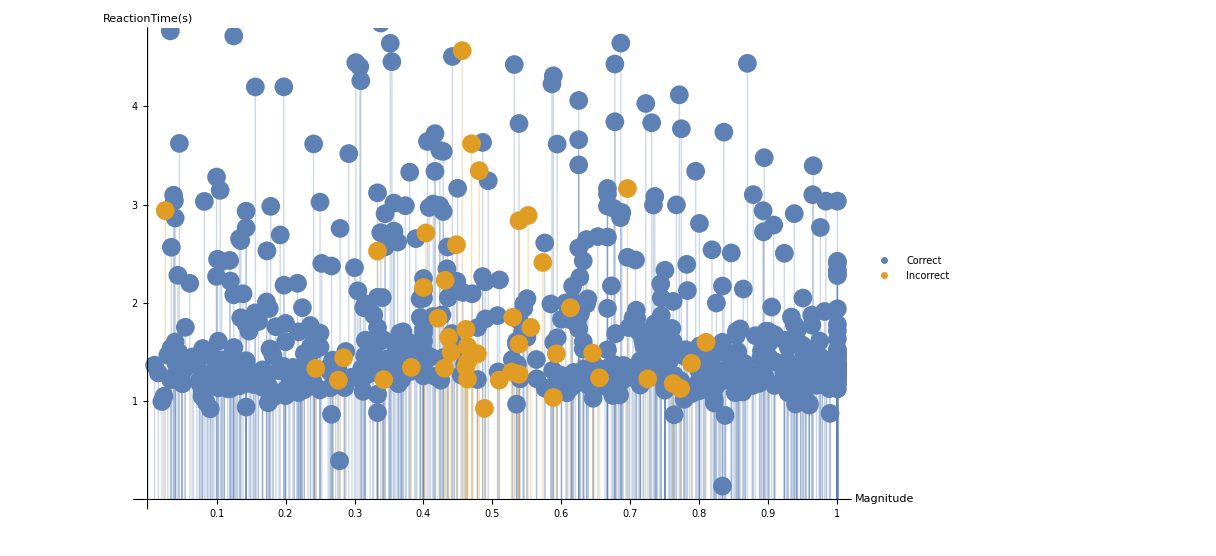

```mathematica
response= filteredData[All,"Response"];
numberResponse=Table[ToExpression[response[i]],{i,1,Length[response]}];
Clear[incorrect];
Clear[correct];
correct={};
Table[Which[
TrueQ[0.5>magnitudes[[i]]],
If[numberResponse[[i]]==0,AppendTo[correct,{magnitudes[[i]],RTs[[i]]}]]
,
TrueQ[0.5<magnitudes[[i]]],
If[numberResponse[[i]]==1,AppendTo[correct,{magnitudes[[i]],RTs[[i]]}]]
],{i,Length[magnitudes]}];
incorrect={};
Table[Which[
TrueQ[0.5>magnitudes[[i]]],
If[numberResponse[[i]]==1,AppendTo[incorrect,{magnitudes[[i]],RTs[[i]]}]]
,
TrueQ[0.5<magnitudes[[i]]],
If[numberResponse[[i]]==0,AppendTo[incorrect,{magnitudes[[i]],RTs[[i]]}]]
],{i,Length[magnitudes]}];
ListPlot[{correct,incorrect},DataRange->{0,1},PlotLegends->{Style["Correct",18,Bold],Style["Incorrect",18,Bold]},PlotStyle->PointSize[.015],AxesLabel->{Style["Magnitude",Large,Bold],Style["ReactionTime(s)",Large,Bold]},Filling->Axis,AxesStyle->Directive[Black,25],ImageSize->900,Ticks->{{.1,.2,.3,.4,.5,.6,.7,.8,.9,1},{1,2,3,4,5,6}}]
```